# VYA - Přednášky

## 1. Přednáška

### Tři důležité příkazy

```mathematica
Quiet[Remove["Global`*"]];
```

Vymaže předchozí definice

```mathematica
$HistoryLength = 2;
```

Omezuje paměť jádra, opatření proti přetečení paměti

```mathematica
SetDirectory[NotebookDirectory[]];
```

SetDir. ~ zavede místo nalezené NotebookDir. ~ cesta k lokaci. jako defaultní adresář

### Struktura výrazu, základy syntaxu

? ~ Help, fomát ? + symbol

```mathematica
?=
```

```mathematica
Vyraz = x+y + Sin[x^2+2*x*y+3]
```

x+y+Sin[3+x^2+2 x y]

```mathematica
Vyraz = x + y + Sin[x^2 + 2xy +3];
```

; ~ Input bez výstupu

```mathematica
?;
```

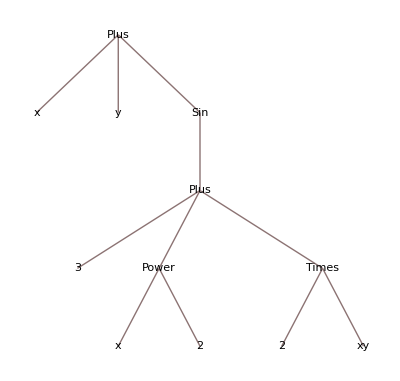

```mathematica
TreeForm[Vyraz]
```

```mathematica
?TreeForm
```

```mathematica
FullForm[Vyraz]
```

Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,xy]]]]

```mathematica
Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,xy]]]]
```

x+y+Sin[3+x^2+2 xy]

```mathematica
?FullForm
```

```mathematica
Head[Vyraz]
```

Plus

```mathematica
?Head
```

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
?Attributes
```

### List

```mathematica
ListTree = {1, {2, 3}, {0,{ A, B}}}
```

{1,{2,3},{0,{A,B}}}

{1,{2,3},{0,{A,B}}}

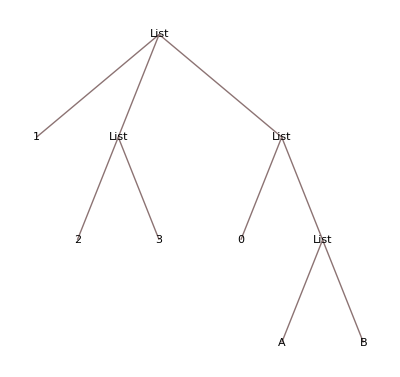

```mathematica
{1,{2,3},{0,{A,B}}}
TreeForm[ListTree]
```

```mathematica
ListTree[[1]]
ListTree[[2]]
ListTree[[3]]
ListTree[[-1]]
```

1

{2,3}

{0,{A,B}}

{0,{A,B}}

```mathematica
ListTree[[0]]
```

List

```mathematica
ListTree[[3, 2, 1]]
```

A

```mathematica
ListTree[[-1,-1,-1]]=C;
ListTree
```

{1,{2,3},{0,{A,C}}}

```mathematica
?Part
```

```mathematica
Length[ListTree]
```

3

```mathematica
?Length
```

```mathematica
Head[ListTree]
ListTree[[0]]
```

List

List

```mathematica
First[ListTree]
ListTree[[1]]
```

1

1

```mathematica
Last[ListTree]
ListTree[[-1]]
```

{0,{A,C}}

{0,{A,C}}

Volání výrazů

```mathematica
{Sin[x], Sin@x, x//Sin}
```

{Sin[x],Sin[x],Sin[x]}

### Souvislost listu a výrazu

```mathematica
TreeForm[Vyraz]
```

-Graphics-

```mathematica
Vyraz[[0]]
Head[Vyraz]
```

Plus

Plus

```mathematica
Vyraz[[1]]
First[Vyraz]
```

x

x

```mathematica
Vyraz[[2]]
Vyraz[[3]]
Vyraz[[-1]]
Last[Vyraz]
```

y

Sin[3+x^2+2 xy]

Sin[3+x^2+2 xy]

Sin[3+x^2+2 xy]

```mathematica
Vyraz[[3, 1]]
```

3+x^2+2 xy

```mathematica
Vyraz[[3, 1, 1]]
Vyraz[[3, 1, 2]]
Vyraz[[3, 1, 2, 1]]
Vyraz[[3, 1, 2, 2]]
Vyraz[[3, 1, 3]]
Vyraz[[3, 1, 3, 1]]
```

3

x^2

x

2

2 xy

2

### Pravidla a programování pomocí nich

```mathematica
x^2 /. x ->2
ReplaceAll[x^2,Rule[x,2]]
```

4

4

/.	=	ReplaceAll
→	=	Rule

```mathematica
?ReplaceAll
```

```mathematica
?Rule
```

```mathematica
x^2 + y /. {x-> E, y ->Pi}
```

ⅇ^2+π

```mathematica
x^2 + y /. {x-> E, y ->Pi, x->C}
```

ⅇ^2+π

```mathematica
1/(I*w*c) /. {c -> 10nF, nF -> 10^-9}
1/(I*w*c) /. {c -> 10nF}
```

-ⅈ/(10 nF w)

-ⅈ/(10 nF w)

```mathematica
1/(I*w*c) //. {c -> 10nF, nF -> 10^-9}
```

-(100000000 ⅈ)/w

//.	=	ReplaceRepeated

```mathematica
?ReplaceRepeated
```

```mathematica
(*x //. {x-> y+x, y -> x}*)
```

```mathematica
x^2 /. {{x -> 2}, {x -> 3}, {x -> 4}}
```

{4,9,16}

==	=	Equal

```mathematica
?Equal
```

```mathematica
Equal[lhs, rhs]
lhs == rhs
```

lhs==rhs

lhs==rhs

```mathematica
{1 == 1, 1 == 2, Equal[1,1], Equal[1,2]}
```

{True,False,True,False}

Pro řešení kořenů rovnice

```mathematica
Rovnice = x^3 + (2 + I)*x^2 + 2I*x + 14 == 0
```

14+2 ⅈ x+(2+ⅈ) x^2+x^3==0

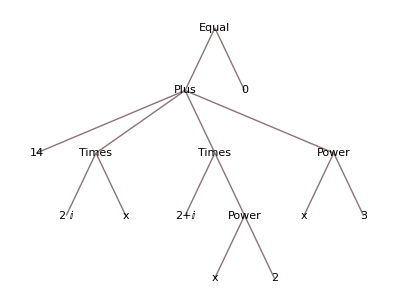

```mathematica
TreeForm[Rovnice]
```

```mathematica
lhs = Rovnice[[1]]
rhs = Rovnice[[2]]
```

14+2 ⅈ x+(2+ⅈ) x^2+x^3

0

```mathematica
Reseni = Solve[Rovnice]
```

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

```mathematica
Rovnice = x^3 + (2 + I)*x^2 + 2I*x + 14. == 0
```

14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0

```mathematica
14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0
Reseni = Solve[Rovnice]
x /. Solve[Rovnice]
```

14.+2 ⅈ x+(2+ⅈ) x^2+x^3==0

{{x→Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176},{x→Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709},{x→Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}}

{Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176,Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709,Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469}

```mathematica
x1 = x /. Reseni[[1]]
x2 = x /. Reseni[[2]]
x3 = x /. Reseni[[3]]
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176

Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

Root0.682-2.40 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,3}]0.6822651721005469

```mathematica
Vysledek = x1 + 2*x2
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
FormVysledku = a + 2*b;
FormVysledku /. {a -> x1, b -> x2}
```

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
Print["x1 + 2*x2 = ", Vysledek]
(x /. Reseni) . {1, 2, 0}
```

x1 + 2*x2 = Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

Root-3.26-0.216 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,1}]-3.2597827730546176+2 Root0.578+1.62 ⅈRoot[{1+#1^2&,14+2 #1 #2+2 #2^2+#1 #2^2+#2^3&},{2,2}]0.5775176009540709

```mathematica
Expres = y - x /. {{x -> 2}, {x -> 3}, {x -> 4}}
Expres /. {List -> Times}
(Expres /. {List -> Times}) /. {y -> x}
Expand[(Expres /. {List -> Times}) /. {y -> x}]
0 == Expand[(Expres /. {List -> Times}) /. {y -> x}]
Reseni = Solve[0 == Expand[(Expres /. {List -> Times}) /. {y -> x}]]
```

{-2+y,-3+y,-4+y}

(-4+y) (-3+y) (-2+y)

(-4+x) (-3+x) (-2+x)

-24+26 x-9 x^2+x^3

0==-24+26 x-9 x^2+x^3

{{x→2},{x→3},{x→4}}

```mathematica
x1 = x /. Reseni[[1]];
x2 = x /. Reseni[[2]];
x3 = x /. Reseni[[3]];
Print["x1 = ", x1]
Print["x2 = ", x2]
Print["x3 = ", x3]
```

x1 = 2

x2 = 3

x3 = 4

```mathematica
Reseni[[1]]
Reseni[[1,1]]
Reseni[[1,1,1]]
Reseni[[1,1,2]]
xRes = {Reseni[[1,1,2]], Reseni[[2,1,2]], Reseni[[3,1,2]]}
```

{x→2}

x→2

x

2

{2,3,4}

```mathematica
Range[100]
Range[100] /. List -> Plus
Range[100] /. List -> Times
N[Range[100] /. List -> Times]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

5050

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

9.33262×10^157

### Patterny

```mathematica
?_
```

```mathematica
?__
```

```mathematica
?___
```

```mathematica
Vyraz = Sin[x^2 + 3] + x^y + E^Pi
```

ⅇ^π+x^y+Sin[3+x^2]

```mathematica
Vyraz /. a_^b_ -> b^a
Vyraz /. a_^b_ :> b^a
```

π^ⅇ+y^x+Sin[3+2^x]

π^ⅇ+y^x+Sin[3+2^x]

```mathematica
?:>
```

```mathematica
Vyraz /. {x^2 -> 2^x, x^y -> y^x}
Vyraz /. x^b_ :> b^x
```

ⅇ^π+y^x+Sin[3+2^x]

ⅇ^π+y^x+Sin[3+2^x]

## 2. Přednáška

```mathematica
Quiet@Remove["Global`*"];
```

### Rule a RuleDelay

```mathematica
Rule[a,b]
a -> b
```

a→b

a→b

```mathematica
RuleDelayed[a,b]
a :> b
```

a:>b

a:>b

:>	=	RuleDelayed

```mathematica
?RuleDelayed
```

```mathematica
Vyraz = Sin[x^2 + 3] + x^y + E^Pi
```

ⅇ^π+x^y+Sin[3+x^2]

```mathematica
a=5;
Vyraz /. a_^b_ :> b^a
Vyraz /. a_^b_ -> b^a
```

π^ⅇ+y^x+Sin[3+2^x]

π^5+y^5+Sin[35]

### Funkce

```mathematica
a = 6;
?a
```

```mathematica
f[x_] := x^2
f[x_,y_] := x^2 + y
```

```mathematica
?f
```

```mathematica
?:=
```

```mathematica
ClearAll[f]
f[x:_] := x^2
f[2]
```

4

```mathematica
ClearAll[f]
f[x_] := x^2
f[2]
?f
```

4

```mathematica
ClearAll[f];
f[x_] := 1+1
?f
```

```mathematica
f[x_] = 1+1
?f
```

2

```mathematica
Ran := Random[]
{Ran, Ran, Ran, Ran}
?Ran
```

{0.884187,0.822339,0.0181411,0.358902}

```mathematica
Ran = Random[]
{Ran, Ran, Ran, Ran}
?Ran
```

0.202024

{0.202024,0.202024,0.202024,0.202024}

```mathematica
ClearAll[f]
x = 5;
f[x_] := x^2
f[2]
f[5]
f[x]
?f
```

4

25

25

```mathematica
ClearAll[f]
x = 5;
f[x_] = x^2
f[2]
f[5]
f[x]
?f
```

25

25

25

«1 more identical outputs»

```mathematica
ClearAll[f, x]
f[x_] = x^2
f[2]
f[5]
f[x]
?f
```

x^2

4

25

x^2

```mathematica
ClearAll[f]
f[x_] := FindRoot[Cos[a*x] == a, {a, 0}]
f[0.5]
```

{6→0.900367}

```mathematica
?FindRoot
```

```mathematica
ClearAll[f,a]
f[x_] = FindRoot[Cos[a*x] == a, {a, 0}]
f[0.5]
```

FindRoot::nlnum: The function value {-1.+Cos[1. x]} is not a list of numbers with dimensions {1} at {a} = {1.}.

{a→0.}

{a→0.}

```mathematica
ClearAll[f]
f[x_] = Integrate[x^0.5 * Sin[x],x]
f[0.1]
```

-(0.5 x^0.5 Gamma[1.5,(0.-1. ⅈ) x])/((0.-1. ⅈ) x)^0.5-(0.5 x^0.5 Gamma[1.5,(0.+1. ⅈ) x])/((0.+1. ⅈ) x)^0.5

-0.625393+0. ⅈ

### Set a SetDelay

www.mathworld.com

```mathematica
ClearAll[f]
f[x_] := Integrate[x^0.5 * Sin[x], x]
f[0.1]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.1.

∫0.0315701ⅆ0.1

```mathematica
ClearAll[f]
f[x_] := x^2
f[0] := 100
f[x_Integer] := 1/x
{f[3], f[3.], f[0], f[3]}
```

{1/3,9.,100,1/3}

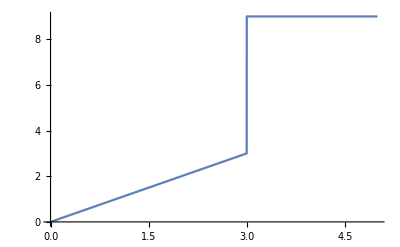

```mathematica
ClearAll[f, Test]
Test[y_] := y <= 3
f[x_?Test] := x
f[x_] := 9
Plot[f[x], {x, 0, 5}]
```

```mathematica
ClearAll[a]
a[n_] := n*a[n-1]
a[0] := 1
a[3]
Trace[a[3]]
```

6

{a[3],3 a[3-1],{{3-1,2},a[2],2 a[2-1],{{2-1,1},a[1],1 a[1-1],{{1-1,0},a[0],1},1 1,1},2 1,2},3 2,6}

```mathematica
?Trace
```

#### Table

```mathematica
Table[predmet, {10}]
```

{predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet,predmet}

```mathematica
?Table
```

```mathematica
Table[x^2, {x,10}]
Table[x^2, {x, 2, 10}]
Table[x^2, {x, 3, 10, 0.2}]
```

{1,4,9,16,25,36,49,64,81,100}

{4,9,16,25,36,49,64,81,100}

{9.,10.24,11.56,12.96,14.44,16.,17.64,19.36,21.16,23.04,25.,27.04,29.16,31.36,33.64,36.,38.44,40.96,43.56,46.24,49.,51.84,54.76,57.76,60.84,64.,67.24,70.56,73.96,77.44,81.,84.64,88.36,92.16,96.04,100.}

```mathematica
ClearAll[a, n, i]
a[n_Integer] := n*a[n-1]
a[0] := 1
Table[a[i], {i, 100}];
Timing[Table[a[i], {i,100}]][[1]]
```

0.015625

```mathematica
?Timing
```

Timing[[1]]	=	Čas potřebný pro výpočet

```mathematica
?$RecursionLimit
```

```mathematica
$RecursionLimit = 10^5;
ClearAll[a, n]
a[n_Integer] := a[n] = n*a[n-1]
a[0] := 1
a[6]
Trace[a[7]]
?a
(*Timing[Table[a[i], {i, 3000}]][[1]]*)
```

720

{a[7],a[7]=7 a[7-1],{{{7-1,6},a[6],720},7 720,5040},a[7]=5040,5040}

### Funkce podmíněně definovaná

```mathematica
Quiet@Remove["Global`*"];
?/;
```

```mathematica
ClearAll[f]
f[x_] := x /; x <= 3
```

```mathematica
f[x_] := 9 /; x > 3
Plot[f[x], {x, 0, 5}]
```

-Graphics-

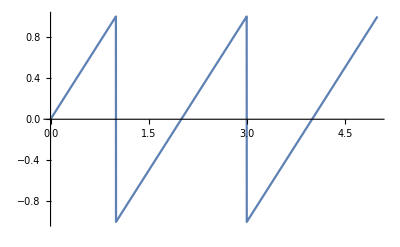

```mathematica
ClearAll[f]
f[x_] := x /; x<= 1
f[x_] := f[x-2] /; x > 1
f[x_] := f[x+2] /; x <= -1
Plot[f[x], {x, 0, 5}]
```

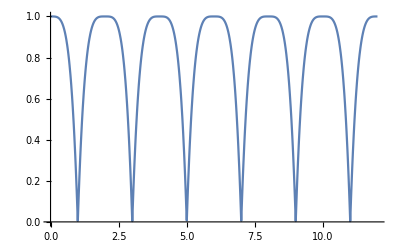

```mathematica
ClearAll[f]
f[x_] := 1 - x^4 /; -1 < x<= 1
f[x_] := f[x-2] /; x > 1
f[x_] := f[x+2] /; x <= -1
Plot[f[x], {x, 0, 12 }]
```

```mathematica
Trace[f[-5.5]]
```

{f[-5.5],{{-1<-5.5≤1,False},RuleCondition[$ConditionHold[$ConditionHold[1-(-5.5)^4]],False],Fail},{{-5.5>1,False},RuleCondition[$ConditionHold[$ConditionHold[f[-5.5-2]]],False],Fail},{{-5.5≤-1,True},RuleCondition[$ConditionHold[$ConditionHold[f[-5.5+2]]],True],$ConditionHold[$ConditionHold[f[-5.5+2]]]},f[-5.5+2],{-5.5+2,-3.5},f[-3.5],{{-1<-3.5≤1,False},RuleCondition[$ConditionHold[$ConditionHold[1-(-3.5)^4]],False],Fail},{{-3.5>1,False},RuleCondition[$ConditionHold[$ConditionHold[f[-3.5-2]]],False],Fail},{{-3.5≤-1,True},RuleCondition[$ConditionHold[$ConditionHold[f[-3.5+2]]],True],$ConditionHold[$ConditionHold[f[-3.5+2]]]},f[-3.5+2],{-3.5+2,-1.5},f[-1.5],{{-1<-1.5≤1,False},RuleCondition[$ConditionHold[$ConditionHold[1-(-1.5)^4]],False],Fail},{{-1.5>1,False},RuleCondition[$ConditionHold[$ConditionHold[f[-1.5-2]]],False],Fail},{{-1.5≤-1,True},RuleCondition[$ConditionHold[$ConditionHold[f[-1.5+2]]],True],$ConditionHold[$ConditionHold[f[-1.5+2]]]},f[-1.5+2],{-1.5+2,0.5},f[0.5],{{-1<0.5≤1,True},RuleCondition[$ConditionHold[$ConditionHold[1-0.5^4]],True],$ConditionHold[$ConditionHold[1-0.5^4]]},1-0.5^4,{{0.5^4,0.0625},-0.0625,-0.0625},1-0.0625,0.9375}

```mathematica
?Which
```

```mathematica
?Piecewise
```

### Formáty parametrů

```mathematica
ClearAll[a]
a[{x_, y_}] := x + y
a[{Pi, 2E}]
```

2 ⅇ+π

### Úkol 2

l---o^vp----------i^vc-->   o-pavouk, i-člověk
Diferenciální rovnice
Člověk utíká od stěny s níž je spojený leteckou gumou, utíká před pavoukem který leze po gumě směrem k němu
vc - rychlost člověka, vůči absolutnímu prostoru
vp - rychlost pavouka,  vůči gumě

## 3. Přednáška

### Používání AI

https://chat.openai.com/

Zadání: “Prosím, napiš skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos, sinus modře a kosínus červeně, popíše osy a graf bude mít GridLines”

Odpoveď: “Samozřejmě, zde je skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos s popisem os a s GridLines:”

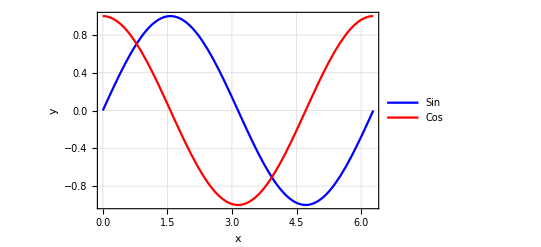

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{Style["x",Bold,14],Style["y",Bold,14]},PlotLegends->{"Sin","Cos"},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400]
```

“Tento skript vykreslí graf funkcí Sin a Cos na intervalu [0, 2 Pi]. Sinus je vykreslen modře a kosinus červeně. Osa x je popsaná nápisem “x” a osa y nápisem “y”. Graf má také mřížky (GridLines) s šedým stylem (GridLinesStyle). Celková velikost grafu je nastavena na 400 pixelů.

Můžete tento skript spustit ve Wolfram Mathematica a zobrazí se vám výsledný graf.”

### Příkaz module

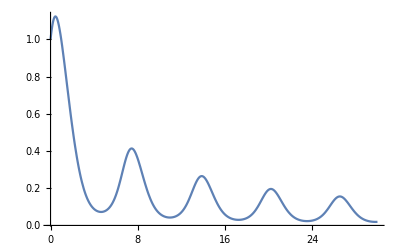

```mathematica
Quiet@Remove["Global`*"];
s[a_] := NDSolve[{y'[x] == y[x] Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}]
g[a_] := Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]
g[1]
```

```mathematica
Quiet@Remove["Global`*"];
f[a_] := Module[{reseni}, reseni = NDSolve[{y'[x] == y[x]Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}];
	Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]]
f[2]
```

1

### Užitečná funkce Tanh

5/2+1/2 Tanh[5 (-4+x)]

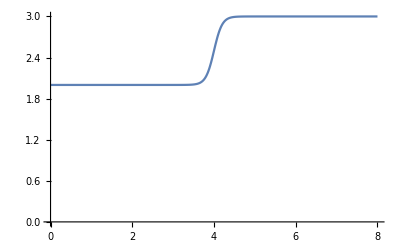

```mathematica
Quiet@Remove["Global`*"];
Prechod[Odkud_, Kam_, Zmena_, Strmost_, Promenna_] := Module[{Rovnice, a, b, Dosaz}, 
Rovnice = {a - b == Odkud, a + b == Kam};
Dosaz = Solve[Rovnice, {a, b}][[1]]; 
a+b*Tanh[Strmost*(Promenna - Zmena)] /. Dosaz];
Graf = Prechod[2, 3, 4, 5, x]
Plot[Graf, {x, 0, 8}, AxesOrigin -> {0, 0}]
```

### Pure functions

```mathematica
Quiet@Remove["Global`*"];
f[x_] := x^2;
f[5]
```

25

```mathematica
?#
```

```mathematica
#^2 & [5]
```

25

```mathematica
g[x_,y_] := x + y^2
g[E, Pi]
```

ⅇ+π^2

```mathematica
#1 + #2^2 & [E, Pi]
```

ⅇ+π^2

```mathematica
h := #1 + #2^2&
h[E, Pi]
```

ⅇ+π^2

```mathematica
?Select
```

```mathematica
Test[x_] := x > 2
Test[1]
Test[3]
Select[{1, 2, 4, 3, 7, 6, 5, 8}, Test]
```

False

True

{4,3,7,6,5,8}

```mathematica
Select[{1, 2, 4, 3, 7, 6, 5, 8}, # > 2 &]
```

{4,3,7,6,5,8}

```mathematica
# > 2 & [1]
```

False

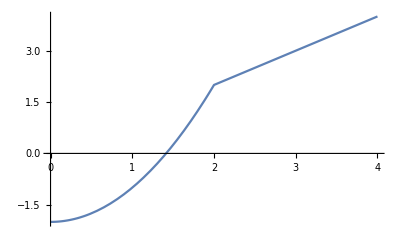

```mathematica
Quiet@Remove["Global`*"];
Test[x_] := x > 2
f[x_?Test] := x
f[x_] := x^2-2
Plot[f[x], {x, 0, 4}]
```

```mathematica
Quiet@Remove["Global`*"];
```

```mathematica
f[x_? (# > 2 &)] := x
f[x_] := x^2-2
Plot[f[x], {x, 0, 4}]
```

-Graphics-

### Map a Apply

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
?Map
```

```mathematica
Map[f, {1, 2, 3, 4}]
f /@ {1, 2, 3, 4}
```

{f[1],f[2],f[3],f[4]}

{f[1],f[2],f[3],f[4]}

```mathematica
Sin[{1, 2, 3, 4}]
```

{Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
Sin /@ {1, 2, 3, 4}
```

{Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

```mathematica
Quiet[Remove["Global`*"]];
?Apply
```

```mathematica
Apply[f, {1, 2, 3, 4}]
f @@ {1, 2, 3, 4}
```

f[1,2,3,4]

f[1,2,3,4]

```mathematica
Apply[f, Map[f, {1, 2, 3, 4}]]
f @@ (f /@ {1, 2, 3, 4})
```

f[f[1],f[2],f[3],f[4]]

f[f[1],f[2],f[3],f[4]]

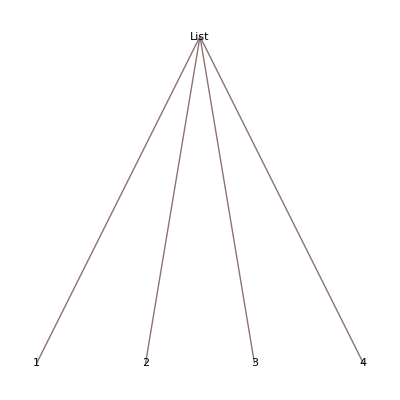
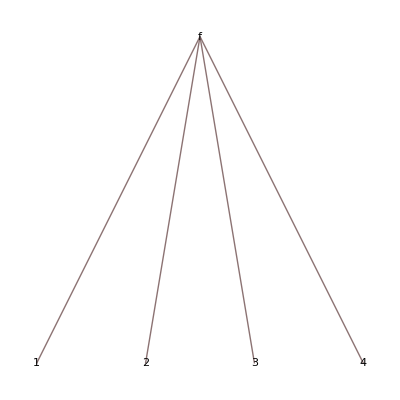

```mathematica
{TreeForm[{1, 2, 3, 4}], TreeForm[f @@ {1, 2, 3, 4}]}
```